```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 210 Kb

{Utilities`CleanSlate`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,Parallel`Debug`Perfmon`,Parallel`Debug`,System`,Global`}

```mathematica
(* Fix this *) 
Clear[l]
l = 0.5 
Clear[d]
d = 0.6
```

0.5

0.6

```mathematica
Clear[q]
q = { θ1[t] , θ2[t] }
```

{θ1[t],θ2[t]}

```mathematica
Clear[r1]
r1 = { l Sin[θ1[t]] , -l Cos[θ1[t]] }
```

{0.5 Sin[θ1[t]],-0.5 Cos[θ1[t]]}

```mathematica
D[r1, t]
```

{0.5 Cos[θ1[t]] θ1'[t],0.5 Sin[θ1[t]] θ1'[t]}

```mathematica
D[r1, t] . D[r1, t]
```

0.25 Cos[θ1[t]]^2 θ1'[t]^2+0.25 Sin[θ1[t]]^2 θ1'[t]^2

```mathematica
D[r1, t] . D[r1, t] // Expand
```

0.25 Cos[θ1[t]]^2 θ1'[t]^2+0.25 Sin[θ1[t]]^2 θ1'[t]^2

```mathematica
D[r1, t] . D[r1, t] // Expand // Simplify
```

0.25 θ1'[t]^2

```mathematica
Clear[r2]
r2 = { d + l Sin[θ2[t]] , -l Cos[θ2[t]] }
```

{0.6+0.5 Sin[θ2[t]],-0.5 Cos[θ2[t]]}

```mathematica
D[r2, t]
```

{0.5 Cos[θ2[t]] θ2'[t],0.5 Sin[θ2[t]] θ2'[t]}

```mathematica
D[r2, t] . D[r2, t]
```

0.25 Cos[θ2[t]]^2 θ2'[t]^2+0.25 Sin[θ2[t]]^2 θ2'[t]^2

```mathematica
D[r2, t] . D[r2, t]  // Expand
```

0.25 Cos[θ2[t]]^2 θ2'[t]^2+0.25 Sin[θ2[t]]^2 θ2'[t]^2

```mathematica
D[r2, t] . D[r2, t]  // Expand  // Simplify
```

0.25 θ2'[t]^2

```mathematica
Clear[T]
T = 1/2 m ( D[r1, t] . D[r1, t]  ) + 1/2 m ( D[r2, t] . D[r2, t]   )  // Expand // Simplify
```

0.+0.125 m θ1'[t]^2+0.125 m θ2'[t]^2

```mathematica
r1
r2
```

{0.5 Sin[θ1[t]],-0.5 Cos[θ1[t]]}

{0.6+0.5 Sin[θ2[t]],-0.5 Cos[θ2[t]]}

```mathematica
√(( r2[[1]] - r1[[1]] )^2+ ( r2[[2]] - r1[[2]])^2) // PowerExpand
```

√((0.5 Cos[θ1[t]]-0.5 Cos[θ2[t]])^2+(0.6-0.5 Sin[θ1[t]]+0.5 Sin[θ2[t]])^2)

```mathematica
( r2[[1]] - r1[[1]] )^2+ ( r2[[2]] - r1[[2]])^2 // Expand // FullSimplify
```

0.86-0.5 Cos[θ1[t]-θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]]

```mathematica
Clear[V1]
V1= 
1/2 k ( Sqrt[ ( r2[[1]] - r1[[1]] )^2+ ( r2[[2]] - r1[[2]])^2 // Expand // FullSimplify  ] -d )^2
```

1/2 k (-0.6+√(0.86-0.5 Cos[θ1[t]-θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]]))^2

```mathematica
Clear[V2]
V2 = - m g l  Cos[θ1[t]] - m g l Cos[θ2[t]] // Simplify
```

g m (-0.5 Cos[θ1[t]]-0.5 Cos[θ2[t]])

```mathematica
Clear[V]
V = V1 + V2
```

g m (-0.5 Cos[θ1[t]]-0.5 Cos[θ2[t]])+1/2 k (-0.6+√(0.86-0.5 Cos[θ1[t]-θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]]))^2

```mathematica
Clear[ℒ]
ℒ = 
T - V ;
ℒ // pdConv
```

-g m (-0.5 cos(θ1(t))-0.5 cos(θ2(t)))-1/2 k (√(-0.5 cos(θ1(t)-θ2(t))-0.6 sin(θ1(t))+0.6 sin(θ2(t))+0.86)-0.6)^2+0.125 m ((∂θ1(t))/(∂t))^2+0.125 m ((∂θ2(t))/(∂t))^2+0.

```mathematica
D[ D[ ℒ , D[q[[1]], t] ] , t ] - D[ ℒ , q[[1]] ] // Expand // Simplify 
D[ D[ ℒ , D[q[[2]], t] ] , t ] - D[ ℒ , q[[2]] ] // Expand // Simplify
```

0.5 g m Sin[θ1[t]]+0.25 k Sin[θ1[t]-θ2[t]]+k Cos[θ1[t]] (-0.3+0.18/(√(0.86-0.5 Cos[θ1[t]-θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]])))-(0.15 k Sin[θ1[t]-θ2[t]])/(√(0.86-0.5 Cos[θ1[t]-θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]]))+0.25 m θ1''[t]

-0.25 k Sin[θ1[t]-θ2[t]]+k Cos[θ2[t]] (0.3-0.18/(√(0.86-0.5 Cos[θ1[t]-θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]])))+(0.15 k Sin[θ1[t]-θ2[t]])/(√(0.86-0.5 Cos[θ1[t]-θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]]))+0.5 g m Sin[θ2[t]]+0.25 m θ2''[t]

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

-0.5 g m Sin[θ1[t]]+(0.3 k (1. Cos[θ1[t]]-0.833333 Sin[θ1[t]-θ2[t]]) (-0.6+√(0.86-0.5 Cos[θ1[t]-θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]])))/(√(0.86-0.5 Cos[θ1[t]-θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]]))-0.25 m θ1''[t]==0
-(0.3 k (1. Cos[θ2[t]]-0.833333 Sin[θ1[t]-θ2[t]]) (-0.6+√(0.86-0.5 Cos[θ1[t]-θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]])))/(√(0.86-0.5 Cos[θ1[t]-θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]]))-0.5 g m Sin[θ2[t]]-0.25 m θ2''[t]==0

```mathematica
Clear[parameters]
parameters = { 
m-> 10 , 
g-> 9.8 , 
k-> 30 , 
l-> 0.5 , 
d-> 0.6 
} ;
parameters // TableForm
```

m→10
g→9.8
k→30
0.5→0.5
0.6→0.6

```mathematica
eqs /. parameters  // TableForm
```

-49. Sin[θ1[t]]+(9. (1. Cos[θ1[t]]-0.833333 Sin[θ1[t]-θ2[t]]) (-0.6+√(0.86-0.5 Cos[θ1[t]-θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]])))/(√(0.86-0.5 Cos[θ1[t]-θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]]))-2.5 θ1''[t]==0
-(9. (1. Cos[θ2[t]]-0.833333 Sin[θ1[t]-θ2[t]]) (-0.6+√(0.86-0.5 Cos[θ1[t]-θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]])))/(√(0.86-0.5 Cos[θ1[t]-θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]]))-49. Sin[θ2[t]]-2.5 θ2''[t]==0

```mathematica
Clear[ics]
ics = { 
θ1[0] == π/12 ,
θ1'[0] == 0.1 , 
θ2[0] == π / 10 , 
θ2'[0] == 0 
} ;
ics // TableForm
```

θ1[0]==π/12
θ1'[0]==0.1
θ2[0]==π/10
θ2'[0]==0

```mathematica
Clear[solution]
solution[t_] = 
First[ NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0, 100 } ] ]
```

{θ1[t]→InterpolatingFunction[…][t],θ2[t]→InterpolatingFunction[…][t]}

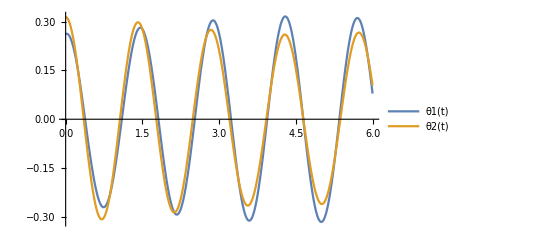

```mathematica
Plot[ Evaluate[ q /. solution[t]]  , { t, 0, 6 } , PlotLegends-> q  ]
```

```mathematica
solution[t]
solution[t][[1]]
solution[t][[1,2]]
```

{θ1[t]→InterpolatingFunction[…][t],θ2[t]→InterpolatingFunction[…][t]}

θ1[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,  { tmax  , 1, 50 , 0.2  } ]
```

```mathematica
solution[t]
solution[t][[2]]
solution[t][[2,2]]
```

{θ1[t]→InterpolatingFunction[…][t],θ2[t]→InterpolatingFunction[…][t]}

θ2[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

```mathematica
Animate[
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, tmax } , AxesLabel-> { q[[2]] , D[q[[2]], t] } ] , { tmax , 0.1, 50 , 0.2 } ]
```

```mathematica
D[ D[ ℒ , D[q[[1]], t] ] , t ]
D[ ℒ , q[[1]] ] // TrigExpand
```

0.25 m θ1''[t]

0.+0.3 k Cos[θ1[t]]-0.5 g m Sin[θ1[t]]-0.25 k Cos[θ2[t]] Sin[θ1[t]]+0.25 k Cos[θ1[t]] Sin[θ2[t]]-(0.18 k Cos[θ1[t]])/(√(0.86-0.5 Cos[θ1[t]] Cos[θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]]-0.5 Sin[θ1[t]] Sin[θ2[t]]))+(0.15 k Cos[θ2[t]] Sin[θ1[t]])/(√(0.86-0.5 Cos[θ1[t]] Cos[θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]]-0.5 Sin[θ1[t]] Sin[θ2[t]]))-(0.15 k Cos[θ1[t]] Sin[θ2[t]])/(√(0.86-0.5 Cos[θ1[t]] Cos[θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]]-0.5 Sin[θ1[t]] Sin[θ2[t]]))

```mathematica
D[ D[ ℒ , D[q[[2]], t] ] , t ]
D[ ℒ , q[[2]] ] // TrigExpand
```

0.25 m θ2''[t]

0.-0.3 k Cos[θ2[t]]+0.25 k Cos[θ2[t]] Sin[θ1[t]]-0.5 g m Sin[θ2[t]]-0.25 k Cos[θ1[t]] Sin[θ2[t]]+(0.18 k Cos[θ2[t]])/(√(0.86-0.5 Cos[θ1[t]] Cos[θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]]-0.5 Sin[θ1[t]] Sin[θ2[t]]))-(0.15 k Cos[θ2[t]] Sin[θ1[t]])/(√(0.86-0.5 Cos[θ1[t]] Cos[θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]]-0.5 Sin[θ1[t]] Sin[θ2[t]]))+(0.15 k Cos[θ1[t]] Sin[θ2[t]])/(√(0.86-0.5 Cos[θ1[t]] Cos[θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]]-0.5 Sin[θ1[t]] Sin[θ2[t]]))

```mathematica
Normal[Series[ Sin[θ1[t]] , { θ1[t] , 0, 1 } ]] 
Normal[Series[ Sin[θ2[t]] , { θ2[t] , 0, 1 } ]]
Normal[Series[ Cos[θ1[t]] , { θ1[t] , 0, 1 } ]]
Normal[Series[ Cos[θ2[t]] , { θ2[t] , 0, 1 } ]]
```

θ1[t]

θ2[t]

1

1

```mathematica
Clear[θReplace]
θReplace = { 
Sin[θ1[t]] -> Normal[Series[ Sin[θ1[t]] , { θ1[t] , 0, 1 } ]]  , 
Sin[θ2[t]] -> Normal[Series[ Sin[θ2[t]] , { θ2[t] , 0, 1 } ]] , 
Cos[θ1[t]] -> Normal[Series[ Cos[θ1[t]] , { θ1[t] , 0, 1 } ]] , 
 Cos[θ2[t]]-> Normal[Series[ Cos[θ2[t]] , { θ2[t] , 0, 1 } ]] 
} ;
θReplace  // TableForm
```

Sin[θ1[t]]→θ1[t]
Sin[θ2[t]]→θ2[t]
Cos[θ1[t]]→1
Cos[θ2[t]]→1

```mathematica
D[ ℒ , q[[1]] ]  // TrigExpand  //. θReplace
```

0.+0.3 k Cos[θ1[t]]-0.5 g m Sin[θ1[t]]-0.25 k Cos[θ2[t]] Sin[θ1[t]]+0.25 k Cos[θ1[t]] Sin[θ2[t]]-(0.18 k Cos[θ1[t]])/(√(0.86-0.5 Cos[θ1[t]] Cos[θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]]-0.5 Sin[θ1[t]] Sin[θ2[t]]))+(0.15 k Cos[θ2[t]] Sin[θ1[t]])/(√(0.86-0.5 Cos[θ1[t]] Cos[θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]]-0.5 Sin[θ1[t]] Sin[θ2[t]]))-(0.15 k Cos[θ1[t]] Sin[θ2[t]])/(√(0.86-0.5 Cos[θ1[t]] Cos[θ2[t]]-0.6 Sin[θ1[t]]+0.6 Sin[θ2[t]]-0.5 Sin[θ1[t]] Sin[θ2[t]]))

```mathematica
Clear[tMax]
tMax = 
nFrames=1000;
frames=Table[Graphics[ {Darker[Red],Disk[r1,0.1],Darker[Blue],Disk[r2,0.1]}/.solution[t] ,PlotRange->{{-2.5,2.5},{-2.5,2.5}},Background->Lighter[Cyan]],{t,tMax/nFrames,tMax,tMax/nFrames}];
ListAnimate[frames]
```